# Enter title here

## Enter subtitle here

Enter subsubtitle here

Enter author here

Enter department here

Enter date here

## Enter section title here

Enter subsection title here
start with the bohr model with the spherical harmonics to represent energy levels
1D, 2D and 3D particle in a box 
use these models to tell us about energy levels and electron position, hi light their correct prediction’s and their limitations

#### Enter subsubsection title here

1 part of the project could be playing around with different ways to plot and use this hydrogen wave function thing, change quantum numbers and plot it different ways to learn about quantum numbers and visualizations (Can this tell us about energy levels?)

```mathematica
PolarPlot[Evaluate[[3,2,0,a,{r,θ,0},{r,4}]],{θ,0,10}]
```

-Graphics-

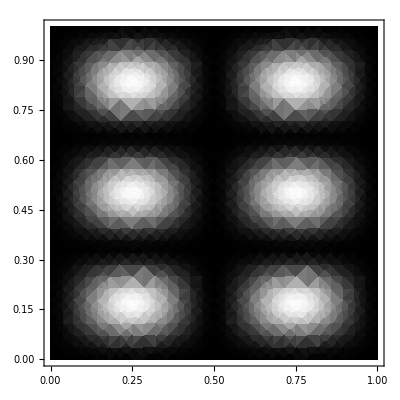

-Graphics-

```mathematica
psi=Sin[2*Pi*x]*Sin[3*Pi*y];
DensityPlot[psi^2,{x,0,1},{y,0,1},ColorFunction->Function[z,Blend[{Black,White},z]]]

psi=Exp[-x^2]*Exp[10*I*x];
Plot[Abs[psi],{x,-3,3},PlotPoints->300,Filling->Axis,ColorFunction->Function[x,Hue[Arg[psi]/(2Pi)]],ColorFunctionScaling->False]
DensityPlot[psi,{x,0,1},{y,0,1},PlotPoints->100,ColorFunction->Function[z,Blend[{Cyan,Black,Red},z]]]
```

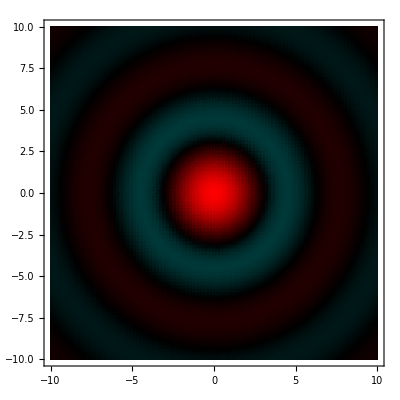

-Graphics-

```mathematica
psi=Sin[Sqrt[x^2+y^2]]/Sqrt[x^2+y^2];
DensityPlot[psi/2+0.5,{x,-10,10},{y,-10,10},PlotRange->All,PlotPoints->100,ColorFunctionScaling->False,ColorFunction->Function[z,Blend[{Cyan,Black,Red},z]]]
psi=Exp[-(x^2+y^2)]*Exp[10*I*(x-y)];
RegionPlot[True,{x,-3,3},{y,-3,3},PlotPoints->100,ColorFunctionScaling->False,ColorFunction->Function[{x,y},Hue[Arg[psi]/(2 Pi),1,Abs[psi]]]]
```

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}